```mathematica
1+1
```

2

```mathematica
(*<<"C:\\Users\\fsiano\\work\\dev\\workspace\\optLNG\\optExhaustiveSearch\\Kernel\\optExhaustiveSearch.m"*)
```

## Input

All volumes in units of m^3
All charging/discharging rates in units of m^3/h
All boil-off rates in units of percentage/day

```mathematica
LNGTerminals=$terminalSpec;
LNGVessels=$vesselSpec;
```

```mathematica
GeoMarker[#["LatLong"]] & /@ LNGTerminals
```

```mathematica
GeoGraphics[GeoMarker[#["LatLong"]] & /@ LNGTerminals, GeoRange->All]
```

```mathematica
GeoGraphics[GeoMarker[#["Position"]] & /@ LNGVessels, GeoRange->All]
```

```mathematica
Dataset[LNGTerminals]
```

Dataset[<>]

```mathematica
Dataset[LNGVessels]
```

Dataset[<>]

```mathematica
GeoDistance[{LNGVessels["WSD50"]["Position"], LNGTerminals["Golden Pass"]["LatLong"]},UnitSystem->"NauticalMiles"]/LNGVessels["WSD50"]["Speed"]
```

278.707 h

```mathematica
{LNGVessels["WSD50"]["Position"], LNGTerminals["Golden Pass"]["LatLong"]}
```

{GeoPosition[{58.97,5.71}],GeoPosition[{29.7616,-93.9292}]}

```mathematica
Tuples[Outer[{#1, #2, #3}&, Keys[LNGVessels], Keys[Select[LNGTerminals, #Type=="Liquification and Export" &]], Keys[Select[LNGTerminals, #Type=="Import and Re-gasification" &]], 1, 1, 1]]
```

```mathematica
v={v1, v2, v3};
p={p1, p2, Missing[]};
m={m1, m2, m3};
```

```mathematica
Tuples[{v, p, m}]
```

{{v1,p1,m1},{v1,p1,m2},{v1,p1,m3},{v1,p2,m1},{v1,p2,m2},{v1,p2,m3},{v1,p3,m1},{v1,p3,m2},{v1,p3,m3},{v2,p1,m1},{v2,p1,m2},{v2,p1,m3},{v2,p2,m1},{v2,p2,m2},{v2,p2,m3},{v2,p3,m1},{v2,p3,m2},{v2,p3,m3},{v3,p1,m1},{v3,p1,m2},{v3,p1,m3},{v3,p2,m1},{v3,p2,m2},{v3,p2,m3},{v3,p3,m1},{v3,p3,m2},{v3,p3,m3}}

```mathematica
Tuples[{v, p}]/. {a_,b_}->a->b
```

{v1→p1,v1→p2,v1→p3,v2→p1,v2→p2,v2→p3,v3→p1,v3→p2,v3→p3}

```mathematica
Graph[Join[Tuples[{v, p}]/. {a_,b_}->a->b, Tuples[{p, m}]/. {a_,b_}->a->b], VertexLabels->"Name"]
```

```mathematica
FindPath[Out[34], v1, m1, Infinity, All]
```

{{v1,p3,m1},{v1,p2,m1},{v1,p1,m1}}

```mathematica
Permutations[v]
```

{{v1,v2,v3},{v1,v3,v2},{v2,v1,v3},{v2,v3,v1},{v3,v1,v2},{v3,v2,v1}}

```mathematica
Permutations[p]
```

{{p1,p2},{p2,p1}}

```mathematica
Permutations[m]
```

{{m1,m2,m3},{m1,m3,m2},{m2,m1,m3},{m2,m3,m1},{m3,m1,m2},{m3,m2,m1}}

```mathematica
DeleteDuplicates[Flatten[Outer[Sort[Transpose[{#1, #2}]]&, Permutations[v], Permutations[p], 1, 1],1 ] ]
```

{{{v1,p1},{v2,p2},{v3,}},{{v1,p1},{v2,},{v3,p2}},{{v1,p2},{v2,p1},{v3,}},{{v1,p2},{v2,},{v3,p1}},{{v1,},{v2,p1},{v3,p2}},{{v1,},{v2,p2},{v3,p1}}}

```mathematica
DeleteDuplicates[Flatten[Outer[Sort[Transpose[{#1, #2}]]&, DeleteDuplicates[Flatten[Outer[Sort[Transpose[{#1, #2}]]&, Permutations[v], Permutations[p], 1, 1],1 ] ], Permutations[m], 1, 1], 1]]
```

{{{{v1,p1},m1},{{v2,p2},m2},{{v3,Missing[]},m3}},{{{v1,p1},m1},{{v2,p2},m3},{{v3,Missing[]},m2}},{{{v1,p1},m2},{{v2,p2},m1},{{v3,Missing[]},m3}},{{{v1,p1},m2},{{v2,p2},m3},{{v3,Missing[]},m1}},{{{v1,p1},m3},{{v2,p2},m1},{{v3,Missing[]},m2}},{{{v1,p1},m3},{{v2,p2},m2},{{v3,Missing[]},m1}},{{{v1,p1},m1},{{v2,Missing[]},m2},{{v3,p2},m3}},{{{v1,p1},m1},{{v2,Missing[]},m3},{{v3,p2},m2}},{{{v1,p1},m2},{{v2,Missing[]},m1},{{v3,p2},m3}},{{{v1,p1},m2},{{v2,Missing[]},m3},{{v3,p2},m1}},{{{v1,p1},m3},{{v2,Missing[]},m1},{{v3,p2},m2}},{{{v1,p1},m3},{{v2,Missing[]},m2},{{v3,p2},m1}},{{{v1,p2},m1},{{v2,p1},m2},{{v3,Missing[]},m3}},{{{v1,p2},m1},{{v2,p1},m3},{{v3,Missing[]},m2}},{{{v1,p2},m2},{{v2,p1},m1},{{v3,Missing[]},m3}},{{{v1,p2},m2},{{v2,p1},m3},{{v3,Missing[]},m1}},{{{v1,p2},m3},{{v2,p1},m1},{{v3,Missing[]},m2}},{{{v1,p2},m3},{{v2,p1},m2},{{v3,Missing[]},m1}},{{{v1,p2},m1},{{v2,Missing[]},m2},{{v3,p1},m3}},{{{v1,p2},m1},{{v2,Missing[]},m3},{{v3,p1},m2}},{{{v1,p2},m2},{{v2,Missing[]},m1},{{v3,p1},m3}},{{{v1,p2},m2},{{v2,Missing[]},m3},{{v3,p1},m1}},{{{v1,p2},m3},{{v2,Missing[]},m1},{{v3,p1},m2}},{{{v1,p2},m3},{{v2,Missing[]},m2},{{v3,p1},m1}},{{{v1,Missing[]},m1},{{v2,p1},m2},{{v3,p2},m3}},{{{v1,Missing[]},m1},{{v2,p1},m3},{{v3,p2},m2}},{{{v1,Missing[]},m2},{{v2,p1},m1},{{v3,p2},m3}},{{{v1,Missing[]},m2},{{v2,p1},m3},{{v3,p2},m1}},{{{v1,Missing[]},m3},{{v2,p1},m1},{{v3,p2},m2}},{{{v1,Missing[]},m3},{{v2,p1},m2},{{v3,p2},m1}},{{{v1,Missing[]},m1},{{v2,p2},m2},{{v3,p1},m3}},{{{v1,Missing[]},m1},{{v2,p2},m3},{{v3,p1},m2}},{{{v1,Missing[]},m2},{{v2,p2},m1},{{v3,p1},m3}},{{{v1,Missing[]},m2},{{v2,p2},m3},{{v3,p1},m1}},{{{v1,Missing[]},m3},{{v2,p2},m1},{{v3,p1},m2}},{{{v1,Missing[]},m3},{{v2,p2},m2},{{v3,p1},m1}}}

```mathematica
(Sort/@Flatten[Outer[(Apply[Join,#] &/@Transpose[{#1, #2}])&,Flatten[Outer[(Apply[Join,#] &/@Transpose[{#1, #2}])&, Permutations[<|"Vessel"->#|> & /@v], Permutations[<|"Production"->#|> & /@p], 1, 1],1 ], Permutations[<|"Market"->#|> & /@m], 1, 1], 1])//DeleteDuplicates
```

{{<|Vessel→v1,Production→p1,Market→m1|>,<|Vessel→v2,Production→p2,Market→m2|>,<|Vessel→v3,Production→Missing[],Market→m3|>},{<|Vessel→v1,Production→p1,Market→m1|>,<|Vessel→v2,Production→p2,Market→m3|>,<|Vessel→v3,Production→Missing[],Market→m2|>},{<|Vessel→v1,Production→p1,Market→m2|>,<|Vessel→v2,Production→p2,Market→m1|>,<|Vessel→v3,Production→Missing[],Market→m3|>},{<|Vessel→v1,Production→p1,Market→m2|>,<|Vessel→v2,Production→p2,Market→m3|>,<|Vessel→v3,Production→Missing[],Market→m1|>},{<|Vessel→v1,Production→p1,Market→m3|>,<|Vessel→v2,Production→p2,Market→m1|>,<|Vessel→v3,Production→Missing[],Market→m2|>},{<|Vessel→v1,Production→p1,Market→m3|>,<|Vessel→v2,Production→p2,Market→m2|>,<|Vessel→v3,Production→Missing[],Market→m1|>},{<|Vessel→v1,Production→p1,Market→m1|>,<|Vessel→v2,Production→Missing[],Market→m2|>,<|Vessel→v3,Production→p2,Market→m3|>},{<|Vessel→v1,Production→p1,Market→m1|>,<|Vessel→v2,Production→Missing[],Market→m3|>,<|Vessel→v3,Production→p2,Market→m2|>},{<|Vessel→v1,Production→p1,Market→m2|>,<|Vessel→v2,Production→Missing[],Market→m1|>,<|Vessel→v3,Production→p2,Market→m3|>},{<|Vessel→v1,Production→p1,Market→m2|>,<|Vessel→v2,Production→Missing[],Market→m3|>,<|Vessel→v3,Production→p2,Market→m1|>},{<|Vessel→v1,Production→p1,Market→m3|>,<|Vessel→v2,Production→Missing[],Market→m1|>,<|Vessel→v3,Production→p2,Market→m2|>},{<|Vessel→v1,Production→p1,Market→m3|>,<|Vessel→v2,Production→Missing[],Market→m2|>,<|Vessel→v3,Production→p2,Market→m1|>},{<|Vessel→v1,Production→p2,Market→m1|>,<|Vessel→v2,Production→p1,Market→m2|>,<|Vessel→v3,Production→Missing[],Market→m3|>},{<|Vessel→v1,Production→p2,Market→m1|>,<|Vessel→v2,Production→p1,Market→m3|>,<|Vessel→v3,Production→Missing[],Market→m2|>},{<|Vessel→v1,Production→p2,Market→m2|>,<|Vessel→v2,Production→p1,Market→m1|>,<|Vessel→v3,Production→Missing[],Market→m3|>},{<|Vessel→v1,Production→p2,Market→m2|>,<|Vessel→v2,Production→p1,Market→m3|>,<|Vessel→v3,Production→Missing[],Market→m1|>},{<|Vessel→v1,Production→p2,Market→m3|>,<|Vessel→v2,Production→p1,Market→m1|>,<|Vessel→v3,Production→Missing[],Market→m2|>},{<|Vessel→v1,Production→p2,Market→m3|>,<|Vessel→v2,Production→p1,Market→m2|>,<|Vessel→v3,Production→Missing[],Market→m1|>},{<|Vessel→v1,Production→p2,Market→m1|>,<|Vessel→v2,Production→Missing[],Market→m2|>,<|Vessel→v3,Production→p1,Market→m3|>},{<|Vessel→v1,Production→p2,Market→m1|>,<|Vessel→v2,Production→Missing[],Market→m3|>,<|Vessel→v3,Production→p1,Market→m2|>},{<|Vessel→v1,Production→p2,Market→m2|>,<|Vessel→v2,Production→Missing[],Market→m1|>,<|Vessel→v3,Production→p1,Market→m3|>},{<|Vessel→v1,Production→p2,Market→m2|>,<|Vessel→v2,Production→Missing[],Market→m3|>,<|Vessel→v3,Production→p1,Market→m1|>},{<|Vessel→v1,Production→p2,Market→m3|>,<|Vessel→v2,Production→Missing[],Market→m1|>,<|Vessel→v3,Production→p1,Market→m2|>},{<|Vessel→v1,Production→p2,Market→m3|>,<|Vessel→v2,Production→Missing[],Market→m2|>,<|Vessel→v3,Production→p1,Market→m1|>},{<|Vessel→v1,Production→Missing[],Market→m1|>,<|Vessel→v2,Production→p1,Market→m2|>,<|Vessel→v3,Production→p2,Market→m3|>},{<|Vessel→v1,Production→Missing[],Market→m1|>,<|Vessel→v2,Production→p1,Market→m3|>,<|Vessel→v3,Production→p2,Market→m2|>},{<|Vessel→v1,Production→Missing[],Market→m2|>,<|Vessel→v2,Production→p1,Market→m1|>,<|Vessel→v3,Production→p2,Market→m3|>},{<|Vessel→v1,Production→Missing[],Market→m2|>,<|Vessel→v2,Production→p1,Market→m3|>,<|Vessel→v3,Production→p2,Market→m1|>},{<|Vessel→v1,Production→Missing[],Market→m3|>,<|Vessel→v2,Production→p1,Market→m1|>,<|Vessel→v3,Production→p2,Market→m2|>},{<|Vessel→v1,Production→Missing[],Market→m3|>,<|Vessel→v2,Production→p1,Market→m2|>,<|Vessel→v3,Production→p2,Market→m1|>},{<|Vessel→v1,Production→Missing[],Market→m1|>,<|Vessel→v2,Production→p2,Market→m2|>,<|Vessel→v3,Production→p1,Market→m3|>},{<|Vessel→v1,Production→Missing[],Market→m1|>,<|Vessel→v2,Production→p2,Market→m3|>,<|Vessel→v3,Production→p1,Market→m2|>},{<|Vessel→v1,Production→Missing[],Market→m2|>,<|Vessel→v2,Production→p2,Market→m1|>,<|Vessel→v3,Production→p1,Market→m3|>},{<|Vessel→v1,Production→Missing[],Market→m2|>,<|Vessel→v2,Production→p2,Market→m3|>,<|Vessel→v3,Production→p1,Market→m1|>},{<|Vessel→v1,Production→Missing[],Market→m3|>,<|Vessel→v2,Production→p2,Market→m1|>,<|Vessel→v3,Production→p1,Market→m2|>},{<|Vessel→v1,Production→Missing[],Market→m3|>,<|Vessel→v2,Production→p2,Market→m2|>,<|Vessel→v3,Production→p1,Market→m1|>}}

### Connect to aquaplot

```mathematica
xxx=URLExecute[HTTPRequest["https://api.aquaplot.com/v1/quota", VerifySecurityCertificates->False]];
```

```mathematica
xxx
```

```mathematica
xxx=URLExecute["https://api.aquaplot.com/v1/quota"]
```

```mathematica
xxx
```

```mathematica
xxx=URLExecute[HTTPRequest["https://api.aquaplot.com/v1/route/from/32.67333984375/33.17434155100208/to/35.92529296875/24.806681353851964"]]
```

```mathematica
URLExecute["http://en.wikipedia.org/w/api.php",{"format"->"json","action"->"query","titles"->"Main Page","prop"->"revisions","rvprop"->"content"}]//Short
```

{batchcomplete→,query→{pages→{15580374→{pageid→15580374,«2»,revisions→{{contentformat→text/x-wiki,«1»,c…el→…}}}}}}

### Make a list of possible decisions

```mathematica
v=Normal[Keys[LNGVessels]];
p=Normal[Keys[Select[LNGTerminals, #Type=="Liquification and Export" &]]];
m=Normal[Keys[Select[LNGTerminals, #Type=="Import and Re-gasification"&]]];
```

```mathematica
{v, p, m}=Module[{len=Max[Length[#]& /@ {v, p, m}]},
PadRight[#, len, Missing[]] & /@ {v, p, m}
];
```

```mathematica
decisions=possibleDecisions[v, p, m];
```

```mathematica
Dimensions[decisions]
```

{288,4}

```mathematica
Length /@ {v, p, m}
```

{4,2,3}

```mathematica
Binomial[288, 30]
```

47701230579106532933000886614512970393712

```mathematica
decisions[[5]]
```

{<|Vessel→Leissner,Production→Missing[],Market→Arun LNG Terminal and Plant Indonesia|>,<|Vessel→Tembek,Production→Missing[],Market→Rudong Jiangsu LNG Terminal China|>,<|Vessel→TGE,Production→PNG LNG Terminal Papua New Guinea,Market→Missing[]|>,<|Vessel→WSD50,Production→Golden Pass,Market→Gate LNG Terminal Netherland|>}

Cashflow one trip

```mathematica
cashflowTrip[#["Vessel"], #["Production"], #["Market"]] & /@ {decisions[[5, 1]]}
```

{<|Vessel→<|Speed→13. nmi/h,Capacity→75000 m^3,Maximum loading rate→1000 m^3/day,Maximum discharge rate→1000 m^3/day,Boil-off rate→0.15,Position→GeoPosition[{5.2234,97.083}],Inventory→0 m^3,DailyFixedCost→200 $|>,Production→Missing[],Market→<|LatLong→GeoPosition[{5.2234,97.083}],Currency→Rupiah,Type→Import and Re-gasification,Total Terminal Storage Capacity→635000 m^3,Price→6.2 $|>,cashflows→-3 319.68 $|>}

```mathematica
{<|"Vessel"-><|"Speed"->Quantity[13., ("NauticalMiles")/("Hours")],"Capacity"->Quantity[75000, ("Meters")^3],"Maximum loading rate"->Quantity[1000, ("Meters")^3/("Days")],"Maximum discharge rate"->Quantity[1000, ("Meters")^3/("Days")],"Boil-off rate"->0.15,"Position"->GeoPosition[{5.2234,97.083}],"Inventory"->Quantity[0, ("Meters")^3],"DailyFixedCost"->Quantity[200, US dollars per day]|>,"Production"->Missing[],"Market"-><|"LatLong"->GeoPosition[{5.2234,97.083}],"Currency"->"Rupiah","Type"->"Import and Re-gasification","Total Terminal Storage Capacity"->Quantity[635000, ("Meters")^3],"Price"->Quantity[6.2, US dollars per meter cubed]|>,"cashflows"->Quantity["-3 319.68", "USDollars"]|>}
```

{<|Vessel→<|Speed→13. nmi/h,Capacity→75000 m^3,Maximum loading rate→1000 m^3/day,Maximum discharge rate→1000 m^3/day,Boil-off rate→0.15,Position→GeoPosition[{5.2234,97.083}],Inventory→0 m^3,DailyFixedCost→200 $|>,Production→Missing[],Market→<|LatLong→GeoPosition[{5.2234,97.083}],Currency→Rupiah,Type→Import and Re-gasification,Total Terminal Storage Capacity→635000 m^3,Price→6.2 $|>,cashflows→-3 319.68 $|>}

```mathematica
cashflowTrip[#["Vessel"], #["Production"], #["Market"]] & /@ {decisions[[5, 4]]}
```

{<|Vessel→<|Speed→15. nmi/h,Capacity→20000 m^3,Maximum loading rate→1250 m^3/day,Maximum discharge rate→1250 m^3/day,Boil-off rate→0.12,Position→GeoPosition[{51.9718,4.0755}],Inventory→0 m^3,DailyFixedCost→100 $|>,Production→<|LatLong→GeoPosition[{29.7616,-93.9292}],Currency→USD,Type→Liquification and Export,Total Terminal Storage Capacity→350000 m^3,Daily Production→5000 m^3/day,Inventory→100000 m^3,Price→4.1 $|>,Market→<|LatLong→GeoPosition[{51.9718,4.0755}],Currency→EUR,Type→Import and Re-gasification,Total Terminal Storage Capacity→540000 m^3,Price→4. $|>,cashflows→13 043.14 $|>}

```mathematica
makeProductionInventory[DateObject[{2018,1,1,3,0,0.},"Instant","Gregorian",0.],DateObject[{2018,1,1,22,0,0.},"Instant","Gregorian",0.], "Hours",Quantity[100000, ("Meters")^3],Quantity[5000, ("Meters")^3/("Days")],Quantity[540000, ("Meters")^3]]
```

TimeSeries[…]

```mathematica
makeProductionInventory[DateObject[{2018, 1, 1, 0, 0, 0.}, CalendarType -> "Gregorian", TimeZone->"Europe/London"],DateObject[{2018, 1, 10, 0, 0}, CalendarType -> "Gregorian", TimeZone->"Europe/London"],"Days",Quantity[100000, ("Meters")^3],Quantity[5000, ("Meters")^3/("Days")],Quantity[540000, ("Meters")^3]]
```

TimeSeries[…]

```mathematica
makeProductionInventory[DateObject[{2018,1,1,3,0,0.},"Instant","Gregorian",0.],DateObject[{2018,1,2,4,0,0.},"Instant","Gregorian",0.],"Days",Quantity[100000, ("Meters")^3],Quantity[5000, ("Meters")^3/("Days")],Quantity[540000, ("Meters")^3]]
```

TimeSeries[…]

```mathematica
makeProductionInventory[DateObject[{2018,1,1,3,0,0.},"Instant","Gregorian",0.],DateObject[{2020,1,1,0,0,0.},"Instant","Gregorian",0.],"Years",Quantity[100000, ("Meters")^3],Quantity[5000, ("Meters")^3/("Days")],Quantity[540000, ("Meters")^3]]
```

<|Tue 1 Jan 2019 03:00:00GMT→540000 m^3|>

```mathematica
Module[{pi=makeProductionInventory[DateObject[{2018,1,1,3,0,0.},"Instant","Gregorian",0.],DateObject[{2018,1,1,22,0,0.},"Instant","Gregorian",0.],"Hours",Quantity[100000, ("Meters")^3],Quantity[5000, ("Meters")^3/("Days")],Quantity[540000, ("Meters")^3]], data},
data=KeyValueMap[List, pi];
TimeSeries[data, ResamplingMethod->{"Interpolation", InterpolationOrder->0}, CalendarType->"Gregorian", TimeZone->"Europe/London"]
(*TimeSeries[data[[All, 2]], {data[[All, 1]]},ResamplingMethod->{"Interpolation", InterpolationOrder->0}, CalendarType->"Gregorian", TimeZone->"Europe/London"]*)
]
```

TimeSeries[…]

```mathematica
$production
```

<|Golden Pass→<|LatLong→GeoPosition[{29.7616,-93.9292}],Currency→USD,Type→Liquification and Export,Total Terminal Storage Capacity→350000 m^3,Daily Production→5000 m^3/day,Inventory→100000 m^3,Price→4.1 $|>,PNG LNG Terminal Papua New Guinea→<|LatLong→GeoPosition[{-9.33862,147.018}],Currency→Kina,Type→Liquification and Export,Total Terminal Storage Capacity→320000 m^3,Daily Production→2500 m^3/day,Inventory→320000 m^3,Price→3.9 $|>|>

```mathematica
valuation[DateObject[{2018, 1, 1}, TimeObject[{0, 0}]], DateObject[{2018, 2, 1}, TimeObject[{0, 0}]], "Days"]
```

<|Golden Pass→<|LatLong→GeoPosition[{29.7616,-93.9292}],Currency→USD,Type→Liquification and Export,Total Terminal Storage Capacity→350000 m^3,Daily Production→5000 m^3/day,Inventory→100000 m^3,Price→TimeSeries[…]|>,PNG LNG Terminal Papua New Guinea→<|LatLong→GeoPosition[{-9.33862,147.018}],Currency→Kina,Type→Liquification and Export,Total Terminal Storage Capacity→320000 m^3,Daily Production→2500 m^3/day,Inventory→320000 m^3,Price→TimeSeries[…]|>|>

```mathematica
$production
```

<|Golden Pass→<|LatLong→GeoPosition[{29.7616,-93.9292}],Currency→USD,Type→Liquification and Export,Total Terminal Storage Capacity→350000 m^3,Daily Production→5000 m^3/day,Inventory→100000 m^3,Price→TimeSeries[…]|>,PNG LNG Terminal Papua New Guinea→<|LatLong→GeoPosition[{-9.33862,147.018}],Currency→Kina,Type→Liquification and Export,Total Terminal Storage Capacity→320000 m^3,Daily Production→2500 m^3/day,Inventory→320000 m^3,Price→TimeSeries[…]|>|>

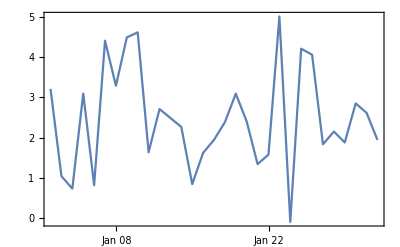

```mathematica
DateListPlot@TimeSeries[…]
```

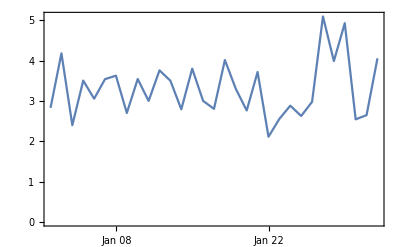

```mathematica
DateListPlot@TimeSeries[…]
```

```mathematica
Ordering[cashflowPlan[#] & /@ decisions, -1][[1]]
```

50

```mathematica
cashflowPlan[decisions[[50]]]
```

<|cashflows→1.3469397377993877e6 $|>

```mathematica
decisions[[50]]
```

{<|Vessel→Leissner,Production→Missing[],Market→Missing[]|>,<|Vessel→Tembek,Production→PNG LNG Terminal Papua New Guinea,Market→Rudong Jiangsu LNG Terminal China|>,<|Vessel→TGE,Production→Missing[],Market→Arun LNG Terminal and Plant Indonesia|>,<|Vessel→WSD50,Production→Golden Pass,Market→Gate LNG Terminal Netherland|>}

```mathematica
cashflowPlan[{<|"Vessel"->"Leissner","Production"->Missing[],"Market"->Missing[]|>,<|"Vessel"->"Tembek","Production"->"PNG LNG Terminal Papua New Guinea","Market"->"Rudong Jiangsu LNG Terminal China"|>,<|"Vessel"->"TGE","Production"->Missing[],"Market"->"Arun LNG Terminal and Plant Indonesia"|>,<|"Vessel"->"WSD50","Production"->"Golden Pass","Market"->"Gate LNG Terminal Netherland"|>}, True, DateObject[{2018, 1, 1}], DateObject[{2019, 1, 1}], "Days"]
```

<|cashflows→1.3469397377993877e6 $|>

```mathematica
valuation[DateObject[{2018, 1, 1}], DateObject[{2019, 1, 1}], "Days"]
```

<|Golden Pass→<|LatLong→GeoPosition[{29.7616,-93.9292}],Currency→USD,Type→Liquification and Export,Total Terminal Storage Capacity→350000 m^3,Daily Production→5000 m^3/day,Inventory→100000 m^3,Price→1|>,PNG LNG Terminal Papua New Guinea→<|LatLong→GeoPosition[{-9.33862,147.018}],Currency→Kina,Type→Liquification and Export,Total Terminal Storage Capacity→320000 m^3,Daily Production→2500 m^3/day,Inventory→320000 m^3,Price→optExhaustiveSearch`Private`makeRandomForwardCurve[1]|>|>
 |  |  |  |

```mathematica
Out[37]["Golden Pass"]
```

<|LatLong→GeoPosition[{29.7616,-93.9292}],Currency→USD,Type→Liquification and Export,Total Terminal Storage Capacity→350000 m^3,Daily Production→5000 m^3/day,Inventory→100000 m^3,Price→optExhaustiveSearch`Private`makeRandomForwardCurve[{Day: Tue 2 Jan 2018,Day: Wed 3 Jan 2018,Day: Thu 4 Jan 2018,Day: Fri 5 Jan 2018,Day: Sat 6 Jan 2018,Day: Sun 7 Jan 2018,Day: Mon 8 Jan 2018,Day: Tue 9 Jan 2018,Day: Wed 10 Jan 2018,Day: Thu 11 Jan 2018,Day: Fri 12 Jan 2018,Day: Sat 13 Jan 2018,Day: Sun 14 Jan 2018,Day: Mon 15 Jan 2018,Day: Tue 16 Jan 2018,Day: Wed 17 Jan 2018,Day: Thu 18 Jan 2018,Day: Fri 19 Jan 2018,Day: Sat 20 Jan 2018,Day: Sun 21 Jan 2018,Day: Mon 22 Jan 2018,Day: Tue 23 Jan 2018,Day: Wed 24 Jan 2018,Day: Thu 25 Jan 2018,Day: Fri 26 Jan 2018,Day: Sat 27 Jan 2018,Day: Sun 28 Jan 2018,Day: Mon 29 Jan 2018,Day: Tue 30 Jan 2018,Day: Wed 31 Jan 2018,Day: Thu 1 Feb 2018,Day: Fri 2 Feb 2018,Day: Sat 3 Feb 2018,Day: Sun 4 Feb 2018,Day: Mon 5 Feb 2018,Day: Tue 6 Feb 2018,Day: Wed 7 Feb 2018,Day: Thu 8 Feb 2018,Day: Fri 9 Feb 2018,Day: Sat 10 Feb 2018,Day: Sun 11 Feb 2018,Day: Mon 12 Feb 2018,Day: Tue 13 Feb 2018,Day: Wed 14 Feb 2018,Day: Thu 15 Feb 2018,Day: Fri 16 Feb 2018,Day: Sat 17 Feb 2018,Day: Sun 18 Feb 2018,Day: Mon 19 Feb 2018,Day: Tue 20 Feb 2018,Day: Wed 21 Feb 2018,Day: Thu 22 Feb 2018,Day: Fri 23 Feb 2018,Day: Sat 24 Feb 2018,Day: Sun 25 Feb 2018,Day: Mon 26 Feb 2018,Day: Tue 27 Feb 2018,Day: Wed 28 Feb 2018,Day: Thu 1 Mar 2018,Day: Fri 2 Mar 2018,Day: Sat 3 Mar 2018,Day: Sun 4 Mar 2018,Day: Mon 5 Mar 2018,Day: Tue 6 Mar 2018,Day: Wed 7 Mar 2018,Day: Thu 8 Mar 2018,Day: Fri 9 Mar 2018,Day: Sat 10 Mar 2018,Day: Sun 11 Mar 2018,Day: Mon 12 Mar 2018,Day: Tue 13 Mar 2018,Day: Wed 14 Mar 2018,Day: Thu 15 Mar 2018,Day: Fri 16 Mar 2018,Day: Sat 17 Mar 2018,Day: Sun 18 Mar 2018,Day: Mon 19 Mar 2018,Day: Tue 20 Mar 2018,Day: Wed 21 Mar 2018,Day: Thu 22 Mar 2018,Day: Fri 23 Mar 2018,Day: Sat 24 Mar 2018,Day: Sun 25 Mar 2018,Day: Mon 26 Mar 2018,Day: Tue 27 Mar 2018,Day: Wed 28 Mar 2018,Day: Thu 29 Mar 2018,Day: Fri 30 Mar 2018,Day: Sat 31 Mar 2018,Day: Sun 1 Apr 2018,Day: Mon 2 Apr 2018,Day: Tue 3 Apr 2018,Day: Wed 4 Apr 2018,Day: Thu 5 Apr 2018,Day: Fri 6 Apr 2018,Day: Sat 7 Apr 2018,Day: Sun 8 Apr 2018,Day: Mon 9 Apr 2018,Day: Tue 10 Apr 2018,Day: Wed 11 Apr 2018,Day: Thu 12 Apr 2018,Day: Fri 13 Apr 2018,Day: Sat 14 Apr 2018,Day: Sun 15 Apr 2018,Day: Mon 16 Apr 2018,Day: Tue 17 Apr 2018,Day: Wed 18 Apr 2018,Day: Thu 19 Apr 2018,Day: Fri 20 Apr 2018,Day: Sat 21 Apr 2018,Day: Sun 22 Apr 2018,Day: Mon 23 Apr 2018,Day: Tue 24 Apr 2018,Day: Wed 25 Apr 2018,Day: Thu 26 Apr 2018,Day: Fri 27 Apr 2018,Day: Sat 28 Apr 2018,Day: Sun 29 Apr 2018,Day: Mon 30 Apr 2018,Day: Tue 1 May 2018,Day: Wed 2 May 2018,Day: Thu 3 May 2018,Day: Fri 4 May 2018,Day: Sat 5 May 2018,Day: Sun 6 May 2018,Day: Mon 7 May 2018,Day: Tue 8 May 2018,Day: Wed 9 May 2018,Day: Thu 10 May 2018,Day: Fri 11 May 2018,Day: Sat 12 May 2018,Day: Sun 13 May 2018,Day: Mon 14 May 2018,Day: Tue 15 May 2018,Day: Wed 16 May 2018,Day: Thu 17 May 2018,Day: Fri 18 May 2018,Day: Sat 19 May 2018,Day: Sun 20 May 2018,Day: Mon 21 May 2018,Day: Tue 22 May 2018,Day: Wed 23 May 2018,Day: Thu 24 May 2018,Day: Fri 25 May 2018,Day: Sat 26 May 2018,Day: Sun 27 May 2018,Day: Mon 28 May 2018,Day: Tue 29 May 2018,Day: Wed 30 May 2018,Day: Thu 31 May 2018,Day: Fri 1 Jun 2018,Day: Sat 2 Jun 2018,Day: Sun 3 Jun 2018,Day: Mon 4 Jun 2018,Day: Tue 5 Jun 2018,Day: Wed 6 Jun 2018,Day: Thu 7 Jun 2018,Day: Fri 8 Jun 2018,Day: Sat 9 Jun 2018,Day: Sun 10 Jun 2018,Day: Mon 11 Jun 2018,Day: Tue 12 Jun 2018,Day: Wed 13 Jun 2018,Day: Thu 14 Jun 2018,Day: Fri 15 Jun 2018,Day: Sat 16 Jun 2018,Day: Sun 17 Jun 2018,Day: Mon 18 Jun 2018,Day: Tue 19 Jun 2018,Day: Wed 20 Jun 2018,Day: Thu 21 Jun 2018,Day: Fri 22 Jun 2018,Day: Sat 23 Jun 2018,Day: Sun 24 Jun 2018,Day: Mon 25 Jun 2018,Day: Tue 26 Jun 2018,Day: Wed 27 Jun 2018,Day: Thu 28 Jun 2018,Day: Fri 29 Jun 2018,Day: Sat 30 Jun 2018,Day: Sun 1 Jul 2018,Day: Mon 2 Jul 2018,Day: Tue 3 Jul 2018,Day: Wed 4 Jul 2018,Day: Thu 5 Jul 2018,Day: Fri 6 Jul 2018,Day: Sat 7 Jul 2018,Day: Sun 8 Jul 2018,Day: Mon 9 Jul 2018,Day: Tue 10 Jul 2018,Day: Wed 11 Jul 2018,Day: Thu 12 Jul 2018,Day: Fri 13 Jul 2018,Day: Sat 14 Jul 2018,Day: Sun 15 Jul 2018,Day: Mon 16 Jul 2018,Day: Tue 17 Jul 2018,Day: Wed 18 Jul 2018,Day: Thu 19 Jul 2018,Day: Fri 20 Jul 2018,Day: Sat 21 Jul 2018,Day: Sun 22 Jul 2018,Day: Mon 23 Jul 2018,Day: Tue 24 Jul 2018,Day: Wed 25 Jul 2018,Day: Thu 26 Jul 2018,Day: Fri 27 Jul 2018,Day: Sat 28 Jul 2018,Day: Sun 29 Jul 2018,Day: Mon 30 Jul 2018,Day: Tue 31 Jul 2018,Day: Wed 1 Aug 2018,Day: Thu 2 Aug 2018,Day: Fri 3 Aug 2018,Day: Sat 4 Aug 2018,Day: Sun 5 Aug 2018,Day: Mon 6 Aug 2018,Day: Tue 7 Aug 2018,Day: Wed 8 Aug 2018,Day: Thu 9 Aug 2018,Day: Fri 10 Aug 2018,Day: Sat 11 Aug 2018,Day: Sun 12 Aug 2018,Day: Mon 13 Aug 2018,Day: Tue 14 Aug 2018,Day: Wed 15 Aug 2018,Day: Thu 16 Aug 2018,Day: Fri 17 Aug 2018,Day: Sat 18 Aug 2018,Day: Sun 19 Aug 2018,Day: Mon 20 Aug 2018,Day: Tue 21 Aug 2018,Day: Wed 22 Aug 2018,Day: Thu 23 Aug 2018,Day: Fri 24 Aug 2018,Day: Sat 25 Aug 2018,Day: Sun 26 Aug 2018,Day: Mon 27 Aug 2018,Day: Tue 28 Aug 2018,Day: Wed 29 Aug 2018,Day: Thu 30 Aug 2018,Day: Fri 31 Aug 2018,Day: Sat 1 Sep 2018,Day: Sun 2 Sep 2018,Day: Mon 3 Sep 2018,Day: Tue 4 Sep 2018,Day: Wed 5 Sep 2018,Day: Thu 6 Sep 2018,Day: Fri 7 Sep 2018,Day: Sat 8 Sep 2018,Day: Sun 9 Sep 2018,Day: Mon 10 Sep 2018,Day: Tue 11 Sep 2018,Day: Wed 12 Sep 2018,Day: Thu 13 Sep 2018,Day: Fri 14 Sep 2018,Day: Sat 15 Sep 2018,Day: Sun 16 Sep 2018,Day: Mon 17 Sep 2018,Day: Tue 18 Sep 2018,Day: Wed 19 Sep 2018,Day: Thu 20 Sep 2018,Day: Fri 21 Sep 2018,Day: Sat 22 Sep 2018,Day: Sun 23 Sep 2018,Day: Mon 24 Sep 2018,Day: Tue 25 Sep 2018,Day: Wed 26 Sep 2018,Day: Thu 27 Sep 2018,Day: Fri 28 Sep 2018,Day: Sat 29 Sep 2018,Day: Sun 30 Sep 2018,Day: Mon 1 Oct 2018,Day: Tue 2 Oct 2018,Day: Wed 3 Oct 2018,Day: Thu 4 Oct 2018,Day: Fri 5 Oct 2018,Day: Sat 6 Oct 2018,Day: Sun 7 Oct 2018,Day: Mon 8 Oct 2018,Day: Tue 9 Oct 2018,Day: Wed 10 Oct 2018,Day: Thu 11 Oct 2018,Day: Fri 12 Oct 2018,Day: Sat 13 Oct 2018,Day: Sun 14 Oct 2018,Day: Mon 15 Oct 2018,Day: Tue 16 Oct 2018,Day: Wed 17 Oct 2018,Day: Thu 18 Oct 2018,Day: Fri 19 Oct 2018,Day: Sat 20 Oct 2018,Day: Sun 21 Oct 2018,Day: Mon 22 Oct 2018,Day: Tue 23 Oct 2018,Day: Wed 24 Oct 2018,Day: Thu 25 Oct 2018,Day: Fri 26 Oct 2018,Day: Sat 27 Oct 2018,Day: Sun 28 Oct 2018,Day: Mon 29 Oct 2018,Day: Tue 30 Oct 2018,Day: Wed 31 Oct 2018,Day: Thu 1 Nov 2018,Day: Fri 2 Nov 2018,Day: Sat 3 Nov 2018,Day: Sun 4 Nov 2018,Day: Mon 5 Nov 2018,Day: Tue 6 Nov 2018,Day: Wed 7 Nov 2018,Day: Thu 8 Nov 2018,Day: Fri 9 Nov 2018,Day: Sat 10 Nov 2018,Day: Sun 11 Nov 2018,Day: Mon 12 Nov 2018,Day: Tue 13 Nov 2018,Day: Wed 14 Nov 2018,Day: Thu 15 Nov 2018,Day: Fri 16 Nov 2018,Day: Sat 17 Nov 2018,Day: Sun 18 Nov 2018,Day: Mon 19 Nov 2018,Day: Tue 20 Nov 2018,Day: Wed 21 Nov 2018,Day: Thu 22 Nov 2018,Day: Fri 23 Nov 2018,Day: Sat 24 Nov 2018,Day: Sun 25 Nov 2018,Day: Mon 26 Nov 2018,Day: Tue 27 Nov 2018,Day: Wed 28 Nov 2018,Day: Thu 29 Nov 2018,Day: Fri 30 Nov 2018,Day: Sat 1 Dec 2018,Day: Sun 2 Dec 2018,Day: Mon 3 Dec 2018,Day: Tue 4 Dec 2018,Day: Wed 5 Dec 2018,Day: Thu 6 Dec 2018,Day: Fri 7 Dec 2018,Day: Sat 8 Dec 2018,Day: Sun 9 Dec 2018,Day: Mon 10 Dec 2018,Day: Tue 11 Dec 2018,Day: Wed 12 Dec 2018,Day: Thu 13 Dec 2018,Day: Fri 14 Dec 2018,Day: Sat 15 Dec 2018,Day: Sun 16 Dec 2018,Day: Mon 17 Dec 2018,Day: Tue 18 Dec 2018,Day: Wed 19 Dec 2018,Day: Thu 20 Dec 2018,Day: Fri 21 Dec 2018,Day: Sat 22 Dec 2018,Day: Sun 23 Dec 2018,Day: Mon 24 Dec 2018,Day: Tue 25 Dec 2018,Day: Wed 26 Dec 2018,Day: Thu 27 Dec 2018,Day: Fri 28 Dec 2018,Day: Sat 29 Dec 2018,Day: Sun 30 Dec 2018,Day: Mon 31 Dec 2018,Day: Tue 1 Jan 2019},2.82288,1.17783]|>

```mathematica
LNGTerminals
```

<|Golden Pass→<|LatLong→GeoPosition[{29.7616,-93.9292}],Currency→USD,Type→Liquification and Export,Total Terminal Storage Capacity→350000 m^3,Daily Production→5000 m^3/day,Inventory→100000 m^3,Price→4.1 $|>,Gate LNG Terminal Netherland→<|LatLong→GeoPosition[{51.9718,4.0755}],Currency→EUR,Type→Import and Re-gasification,Total Terminal Storage Capacity→540000 m^3,Price→4. $|>,Arun LNG Terminal and Plant Indonesia→<|LatLong→GeoPosition[{5.2234,97.083}],Currency→Rupiah,Type→Import and Re-gasification,Total Terminal Storage Capacity→635000 m^3,Price→6.2 $|>,Rudong Jiangsu LNG Terminal China→<|LatLong→GeoPosition[{32.5292,121.428}],Currency→Yuan Renminbi,Type→Import and Re-gasification,Total Terminal Storage Capacity→680000 m^3,Price→6.5 $|>,PNG LNG Terminal Papua New Guinea→<|LatLong→GeoPosition[{-9.33862,147.018}],Currency→Kina,Type→Liquification and Export,Total Terminal Storage Capacity→320000 m^3,Daily Production→2500 m^3/day,Inventory→320000 m^3,Price→3.9 $|>|>

```mathematica
TimeSeries[With[{dates=DateRange[DateObject[{2018, 1, 1}], DateObject[{2018, 12, 31}], {1, "Days"}]},
Transpose[{dates, Quantity[RandomReal[NormalDistribution[3.9, 0.9]], "USDollars"/"Meters"^3] & /@ Range[Length[dates]]}]
],ResamplingMethod->{"Interpolation",InterpolationOrder->0}]
```

TimeSeries[…]

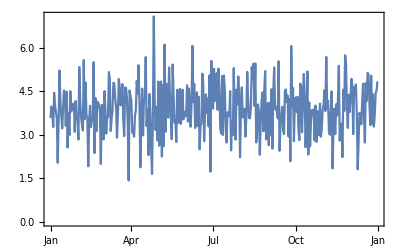

```mathematica
DateListPlot@TimeSeries[…]
```

```mathematica
xxx=<|"a"-><|"n"->1, "p"->""|>, "b"-><|"n"->2, "p"->""|>, "c"-><|"n"->3, "p"->""|>|>
```

<|a→<|n→1,p→|>,b→<|n→2,p→|>,c→<|n→3,p→|>|>

```mathematica
Map[Function[asso, Association[KeyValueMap[If[#1=="p", #1-> Pi, #1->#2 ] &, asso]]][#] &, xxx]
```

<|a→<|n→1,p→π|>,b→<|n→2,p→π|>,c→<|n→3,p→π|>|>

## Junk

### Define the region of all seas.

https://mathematica.stackexchange.com/questions/104407/geographics-path-within-a-country/104416#104416

```mathematica
TravelDirections[{GeoPosition[{29.761564,-93.929215}], GeoPosition[{51.9718, 4.0755}]}]
```

TravelDirections::noroute: Cannot compute path with travel method Driving between locations {GeoPosition[{29.7616,-93.9292}],GeoPosition[{51.9718,4.0755}]}.

$Failed

```mathematica
GeoGraphics[GeoMarker @ {GeoPosition[{29.761564,-93.929215}], GeoPosition[{39.761564,-93.929215}]}]
```

```mathematica
TravelDirections[{GeoPosition[{29.761564,-93.929215}], GeoPosition[{39.76156,-93.929215}]}, TravelMethod->"Walking"]
```

TravelDirectionsData[…]

```mathematica
GeoGraphics[LinguisticAssistant]
```

```mathematica
poly=Entity["Ocean","AtlanticOcean"]["Polygon"]
```

Polygon[GeoPosition[…]]

```mathematica
Entity["Ocean","AtlanticOcean"]
```

Atlantic Ocean

```mathematica
allPonds=GeoGroup[{Entity["Ocean","AtlanticOcean"], Entity["Ocean","AdriaticSea"],Entity["Ocean","AegeanSea"],Entity["Ocean","AlboranSea"],Entity["Ocean","ArgentineSea"],Entity["Ocean","BayBiscay"],Entity["Ocean","BayBothnia"],Entity["Ocean","BayCampeche"],Entity["Ocean","BayFundy"],Entity["Ocean","BalticSea"],Entity["Ocean","BlackSea"],Entity["Ocean","BothnianSea"],Entity["Ocean","CaribbeanSea"],Entity["Ocean","CelticSea"],Entity["Ocean","CentralBalticSea"],Entity["Ocean","ChesapeakeBay"],Entity["Ocean","EnglishChannel"],Entity["Ocean","GulfBothnia"],Entity["Ocean","GulfGuinea"],Entity["Ocean","GulfFinland"],Entity["Ocean","GulfMexico"],Entity["Ocean","GulfSidra"],Entity["Ocean","GulfSaintLawrence"],Entity["Ocean","GulfVenezuela"],Entity["Ocean","IonianSea"],Entity["Ocean","LigurianSea"],Entity["Ocean","IrishSea"],Entity["Ocean","MarmaraSea"],Entity["Ocean","MediterraneanSea"],Entity["Ocean","MirtoonSea"],Entity["Ocean","NorthSea"],Entity["Ocean","SeaAzov"],Entity["Ocean","SeaCrete"],Entity["Ocean","SeaTheHebrides"],Entity["Ocean","SargassoSea"],Entity["Ocean","TampaBay"],Entity["Ocean","ThracianSea"],Entity["Ocean","TyrrhenianSea"],,}]
```

GeoGroup[{Atlantic Ocean,Adriatic Sea,Aegean Sea,Alboran Sea,Argentine Sea,Bay of Biscay,Bay of Bothnia,Bay of Campeche,Bay of Fundy,Baltic Sea,Black Sea,Bothnian Sea,Caribbean Sea,Celtic Sea,Central Baltic Sea,Chesapeake Bay,English Channel,Gulf of Bothnia,Gulf of Guinea,Gulf of Finland,Gulf of Mexico,Gulf of Sidra,Gulf of Saint Lawrence,Gulf of Venezuela,Ionian Sea,Ligurian Sea,Irish Sea,Marmara Sea,Mediterranean Sea,Mirtoon Sea,North Sea,Sea of Azov,Sea of Crete,Sea of Hebrides,Sargasso Sea,Tampa Bay,Thracian Sea,Tyrrhenian Sea}]

```mathematica
poly=Entity["Ocean","AtlanticOcean"]["Polygon"]
```

Polygon[GeoPosition[…]]

```mathematica
pts=Flatten[poly[[1, 1]], 1];
```

```mathematica
line=Polygon[Range[##]]&@@@Partition[{1}~Join~Most[Riffle[Accumulate[Length/@#],1+Accumulate[Length/@#]]&@poly[[1,1]]],2];
```

```mathematica
aquifer=Quiet@DiscretizeRegion[MeshRegion[pts,line],MaxCellMeasure->.004];
```

```mathematica
GeoGraphics[aquifer]
```

```mathematica
allPonds=Cases[Union[Flatten[Join[EntityClass["Ocean","SevenSeas"][EntityProperty["Ocean","BorderingBodiesOfWater"]], EntityClass["Ocean","SevenSeas"][EntityProperty["Ocean","Basins"]]], 1]], Entity[___]]
```

{Adriatic Sea,Aegean Sea,Alboran Sea,Amundsen Gulf,Andaman Sea,Arabian Sea,Arafura Sea,Argentine Sea,Baffin Bay,Balearic Sea,Bali Sea,Baltic Sea,Banda Sea,Barents Sea,Bay of Bengal,Bay of Biscay,Bay of Bothnia,Bay of Campeche,Bay of Fundy,Beaufort Sea,Bering Sea,Bismarck Sea,Black Sea,Bohai Sea,Bohol Sea,Bothnian Sea,Cambridge Bay,Camotes Sea,Caribbean Sea,Celebes Sea,Celtic Sea,Central Baltic Sea,Ceram Sea,Chesapeake Bay,Chilean Sea,Chukchi Sea,Coastal Waters Of Southeast Alaska and British Columbia,Cold Bay,Coral Sea,Davis Strait,Denmark Strait,East China Sea,East Siberian Sea,English Channel,Flores Sea,Great Australian Bight,Greenland Sea,Gulf of Aden,Gulf of Alaska,Gulf of Bothnia,Gulf of California,Gulf of Carpentaria,Gulf of Finland,Gulf of Guinea,Gulf of Mexico,Gulf of Saint Lawrence,Gulf of Sidra,Gulf of Thailand,Gulf of Venezuela,Halmahera Sea,Hudson Bay,Indian Ocean,Inner Seas Off the West Coast of Scotland,Ionian Sea,Irish Sea,James Bay,Sea of Japan,Java Sea,Kara Sea,Kara Strait,Koro Sea,Labrador Sea,Laccadive Sea,Laptev Sea,Ligurian Sea,Lincoln Sea,Marmara Sea,Mediterranean Sea,Mirtoon Sea,Molucca Sea,Mozambique Channel,North Atlantic Ocean,North Pacific Ocean,North Sea,Northwest Passages,Norwegian Sea,Okhotsk Sea,Persian Gulf,Philippine Sea,Red Sea,Rio De La Plata,Salish Sea,Sargasso Sea,Savu Sea,Sea of Azov,Sea of Crete,Sea of Hebrides,Seto Inland Sea,Solomon Sea,South Atlantic Ocean,South China Sea,Southern Ocean,South Pacific Ocean,Strait of Gibraltar,Sulu Sea,Tampa Bay,Tasman Sea,Thracian Sea,Timor Sea,Tyrrhenian Sea,White Sea,Yellow Sea}